```mathematica
{Re[Exp[-I psi]T]/Cos[psi], -Re[Exp[-I psi]TD]/Cos[psi], Re[Exp[-I psi]m]/Cos[psi]}/.{TD->ZLV[{-1,0,0,0},T,m]}/.{T->s+I t,m->m1+I m2}
Simplify[ComplexExpand[%]]
t/.Last@Simplify[Solve[Thread[%=={x,y,mu}],{s,t,m1}]]
Simplify[Reduce[{%>m2,0<=psi<Pi/2,m2>=0},y]]
```

{Re[ⅇ^(-ⅈ psi) (s+ⅈ t)] Sec[psi],-Re[ⅇ^(-ⅈ psi) (-1/2 (m1+ⅈ m2)^2+(m1+ⅈ m2) (s+ⅈ t)+4 (s+ⅈ t)^2)] Sec[psi],Re[ⅇ^(-ⅈ psi) (m1+ⅈ m2)] Sec[psi]}

{s+t Tan[psi],1/2 (m1^2-m2^2-2 m1 s-8 s^2+2 m2 t+8 t^2)+(m1 (m2-t)-s (m2+8 t)) Tan[psi],m1+m2 Tan[psi]}

1/8 Cos[psi]^2 (-m2-m2 Tan[psi]^2+√(Sec[psi]^2 (9 m2^2-8 mu^2+16 mu x+64 x^2+16 y+9 m2^2 Tan[psi]^2)))

(mu|x)∈ℝ&&m2≥0&&psi≥0&&2 psi<π&&y>1/4 (18 m2^2+mu^2-2 mu x-8 x^2+(mu^2-2 mu x-8 x^2) Cos[2 psi]) Sec[psi]^2

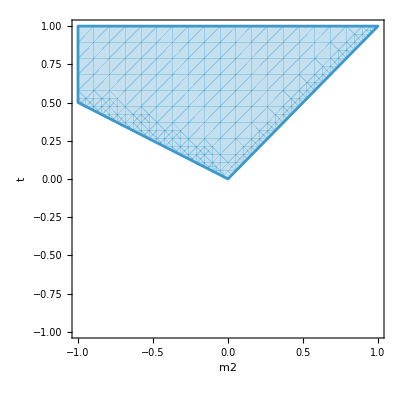

```mathematica
RegionPlot[2t+m2>0&&t-m2>0,{m2,-1,1},{t,-1,1},Axes->True,AxesLabel->Automatic]
```

```mathematica
Reduce[2t2+m2>0&&t2-m2>0,t2]
```

(m2≤0&&t2>-m2/2)||(m2>0&&t2>m2)

```mathematica
y-1/4 (18 m2^2+mu^2-2 mu x-8 x^2+(mu^2-2 mu x-8 x^2) Cos[2 psi]) Sec[psi]^2
```

y-1/4 (18 m2^2+mu^2-2 mu x-8 x^2+(mu^2-2 mu x-8 x^2) Cos[2 psi]) Sec[psi]^2

```mathematica
Solve[r y+(2dF+dB)x+(dF-dB)mu-ch2==0,y]
```

{{y→(ch2+dB mu-dF mu-dB x-2 dF x)/r}}

```mathematica
Solve[r y+(2dF+dB)x+(dF-dB)mu-ch2==0,x]
```

{{x→(ch2+dB mu-dF mu-r y)/(dB+2 dF)}}

```mathematica
Clear[XYRay];
XYRay[{r_,dF_,dB_,ch2_},mu_,z_]:={r z,-(2dF+dB)z}+If[r!=0,{0,(ch2+dB mu-dF mu)/r}, {(ch2+dB mu-dF mu)/(dB+2 dF),0}];
```

```mathematica
XYRay[-Ch[2,-2]/.repCh,-1/10,z]
```

{-z,-28/5+2 z}

```mathematica
Simplify[r y+(2dF+dB)x+(dF-dB)mu-ch2/.{x->t r +Bx,y->-(2dF+dB)t+By}]
```

-ch2+Bx (dB+2 dF)-dB mu+dF mu+By r

{Ch[-3,-2],Ch[-2,-2],Ch[-2,-1],Ch[-1,-1],Ch[0,0],Ch[1,0],Ch[1,1],Ch[2,1],Ch[3,2],Ch[4,2],Ch[4,3],Ch[5,3]}

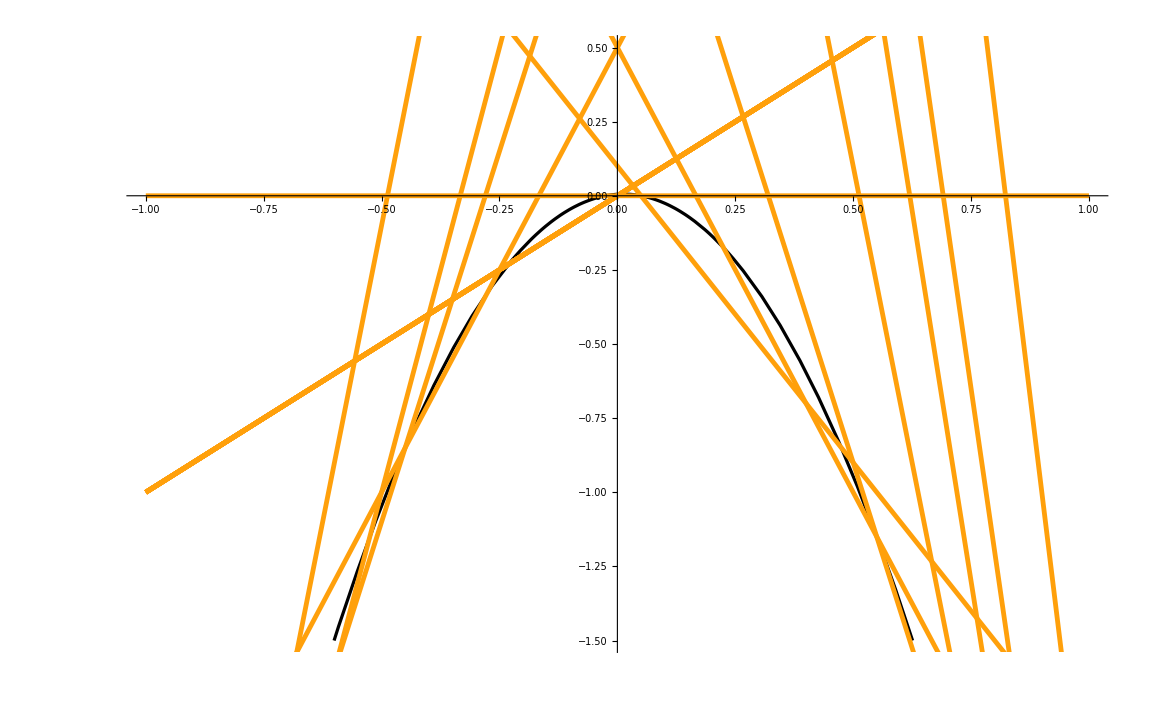

```mathematica
With[{mu=-1/10,m2=0,psi=0},Module[{helixGam,labeledHelixRays},
helixGam={Ch[0,0],Ch[1,0],Ch[1,1],Ch[2,1]};
helixGam = Echo@Flatten[Table[helixGam/.{Ch[p_,q_]:>Ch[p+3k,q+2k]},{k,-1,1}]];

labeledHelixRays = Table[Tooltip[XYRay[c/.repCh, mu,z], c], {c,helixGam}];

Show[
Plot[XYParabolaY[x,mu,m2,psi], {x,-1,1},
PlotStyle->Directive[Thickness[.002],Black],
PlotRange->{{-1,1},{-3/2,1/2}},
GridLines->{{-1/2,1/2},None},
GridLinesStyle->
],
Plot[labeledHelixRays, {z,-1,1},
PlotStyle->Directive[Thickness[.003],RGBColor[1, 0.626, 0.042]]
]
]
]]
```